```mathematica
(*这里计算的是输入的pion介子的GPD，两部分分别是H(β,0,t)的不同形式，参数与之前的note中尽量一致，只有H(β,0,t)的参数相对文献变化为ab1cd对应αβγδ*)
```

```mathematica
Hq=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ^2);
```

```mathematica
Hqn=Hq/.{a->0.7,b1->2.03,c->13.8,d->2,Nv->1/2,b0->2,ξ->0.3,λ->0.79,t->-1};
```

```mathematica
a11=Assuming[x>-0.3&&x<0.3,Integrate[Hqn,{β,-1,1},{α,Abs[β]-1,Abs[β]+1}]];
```

```mathematica
a11/.{x->0.1}
```

0.747765-0.61608 ⅈ

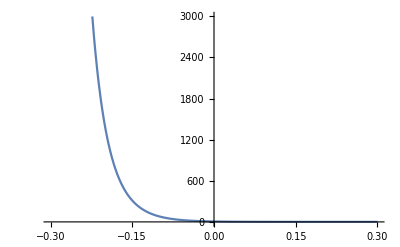

```mathematica
Plot[Re[a11],{x,-0.3,0.3}]
```

```mathematica
1/2*2.6*x^(0.75-1)*(1-x)^0.95
```

```mathematica
Hq2=DiracDelta[x-β-ξ*α]*(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*1/2*2.6*β^(0.75-1)*(1-β)^0.95/(1-t/λ^2);
```

```mathematica
Hqn2=Hq2/.{b0->2,ξ->0.3,λ->0.79,t->-1}
```

(0.468334 (1-β)^0.95 (-α^2+(1-Abs[β])^2)^2 DiracDelta[x-0.3 α-β])/(β^0.25 (1-Abs[β])^5)

```mathematica
a22=Assuming[x>-0.3&&x<0.3,Integrate[Hqn2,{β,-1,1},{α,Abs[β]-1,Abs[β]+1}]];
```

```mathematica
a22/.{x->0.1}
```

1.25485-0.616143 ⅈ

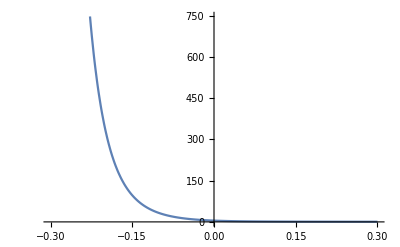

```mathematica
Plot[Re[a22],{x,-0.3,0.3}]
```